# Fully implicit scheme for quasireversible CV

Version 1.30
copyright © 2002-Year Michael Honeychurch

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤

AppendTo[$Path,"(*path to SERM *)/SERM/Data/DigiSimdata"];

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
FrameLabel-> {
Style["increment",FontFamily-> "Arial" ,FontSize->  12,FontColor->Black],
Style["√πχ",FontFamily->  "Times New Roman" ,FontSize->   12, FontWeight->   "Plain",FontColor-> Black],
None,
None},
PlotRange-> {{1,All},{-0.5,0.4}},
PlotStyle-> {Red,AbsoluteThickness[0.5]}
};
```

```mathematica
optionB={
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
StyleForm["√πχ",FontFamily-> "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None},
PlotRange->{{upperLimit+1,lowerLimit-1},{-0.5,0.5}},
PlotStyle->{Red,AbsoluteThickness[0.7]}};
```

```mathematica
optionC={
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
StyleForm["√πχ(at)",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain",FontSlant->"Italic"],
None,
None},
FrameTicks->Automatic,
Joined->{True,True},
PlotStyle-> {Red,Black}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

## Set Up Solution

```mathematica
Clear[implicitSolveIrrevCV];

implicitSolveIrrevCV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_}]:=Module[{x,y,z,len,mat,y1,z1,initial,range,τ,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];

tmp=ξ^α/(3.*ξ^α+ 2*ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*2*ksStar*ξ^(1.-α));
b⟦-1⟧+=d;
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(2*ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,upperLimit,lowerLimit,𝕥];

α=0.5 (*transfer coefficient*);

lowerLimit=-15.5766(*limit = f×(E-E^o)*);

upperLimit=11.6435(*limit = f×(E-E^o)*);

𝕥=2.*(upperLimit+Abs[lowerLimit]);
```

### Simulation variables

```mathematica
Clear[n,𝔻,τ,ksDim,ksStar,m];

n=Round[𝕥/(.002*f)];(*2mV steps*);

𝔻=2.;

τ=𝕥/(n-1) (*calculation of the incremental time/potential step*);

ksDim=0.05067499197462936;(*dimensionless rate constant*)

ksStar=ksDim*Sqrt[𝕥/(𝔻*(n-1))];

m=1+Ceiling[6*√(𝔻*(n-1))];
```

## Solve

```mathematica
Clear[c];
c=implicitSolveIrrevCV[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α}];//Timing
```

{0.17777,Null}

## Plot CV

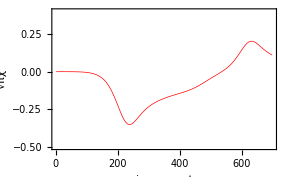

```mathematica
cv1=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*√(𝔻*(n-1))/√(𝕥*4))&,c];
plot1=ListPlot[cv1,optionA]
```

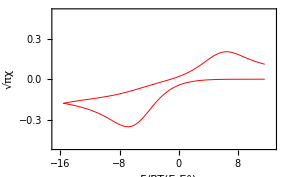

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionB]
```

### Comparison to DigiSim data

```mathematica
mke=Import["logk-3.dat","Table"];
```

k_s=k_s/(σD_O)^(1/2)

```mathematica
A=1.;
𝒟=1.*^-5;
υ=1.;
c1=1.*^-6;
ks=1.*^-3;

kDim=ks/Sqrt[f*1.*𝒟]
```

0.0506878

```mathematica
A=1.;
𝒟=1.*^-5;
υ=1.;
c1=1.*^-6;
ks=1.*^-3;

kDim=ks/Sqrt[f*1.*𝒟];

values=F*A*c1*Sqrt[(𝒟*F*υ)/(R*T)];
mke1=Map[{#⟦1⟧*F/(R*T),-#⟦2⟧/values}&,mke];
```

```mathematica
(*dimensionless potential scan limits. This data is in one millivolt steps*)

Max[mke1⟦All,1⟧]
Min[mke1⟦All,1⟧]
```

11.6765

-15.5687

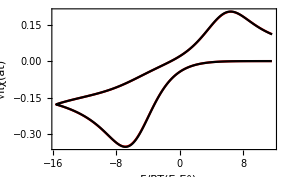

```mathematica
ListPlot[{cv2,mke1},optionC]
```

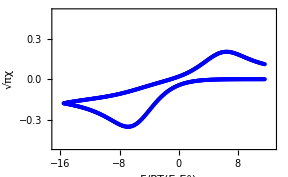

```mathematica
ListPlot[mke1,optionB,Epilog-> {PointSize[0.01],Blue,Point/@cv2}]
```